# Generalized quiver mutations and single centered indices

Jan Manschot, Boris Pioline and Ashoke Sen, Sept. 2013, updated to CoulombHiggs 6.0, Dec 2020

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<CoulombHiggs`
```

CoulombHiggs 6.0 - A package for evaluating quiver invariants

## Examples of ordinary quiver mutations

### Examples 1 and 2: 3-node quiver

```mathematica
aa=2;bb=2;cc=2;
Nvec={2,1,1};
Cvec={-31,10 Nvec[[1]]/Nvec[[2]]+2/Nvec[[2]],21 Nvec[[1]]/Nvec[[3]]-2/Nvec[[3]]};
```

```mathematica
aa=3;bb=4;cc=5;
Nvec={4,1,1};
Cvec={-571,256 Nvec[[1]]/Nvec[[2]]+1/Nvec[[2]],315 Nvec[[1]]/Nvec[[3]]-1/Nvec[[3]]};
```

```mathematica
Mat=({{0, aa, -cc}, {-aa, 0, bb}, {cc, -bb, 0}});
$QuiverMultiplier=1;
$QuiverMultiplierAssumption={};
$QuiverOmSbasis=1;
$QuiverMutationMult=1;
{Mat2,Cvec2,Nvec2}=Simplify[MutateRight[Mat,Cvec,Nvec,1]]
```

{{{0,-3,5},{3,0,-11},{-5,11,0}},{571,1025,-1596},{1,1,1}}

```mathematica
QCoulomb1=DropFugacity[CoulombBranchFormula[Mat,Cvec,Nvec]];
```

```mathematica
QCoulomb2=OmSToOmS2[DropFugacity[CoulombBranchFormula[Mat2,Cvec2,Nvec2]]];
```

```mathematica
Simplify[{QCoulomb1,QCoulomb2}]
```

{OmS[{2,1,1},t]-((1+y^2) OmS[{3,1,1},t])/y+OmS[{4,1,1},t],OmS2[{1,1,1},t]}

```mathematica
Simplify[DropOmSNeg[MutateRightOmS[Mat,1,QCoulomb1]]-QCoulomb2/.OmS2[{0,1,1},t]->0]
```

0

### Example 3: 4-node quiver

```mathematica
aa=5;bb=5;cc=2;dd=1;
Nvec={1,1,1,2};
Cvec={(250 Nvec[[4]]+1)/Nvec[[1]],(170Nvec[[4]]+2)/Nvec[[2]],(30 Nvec[[4]]-3)/Nvec[[3]],-450};
```

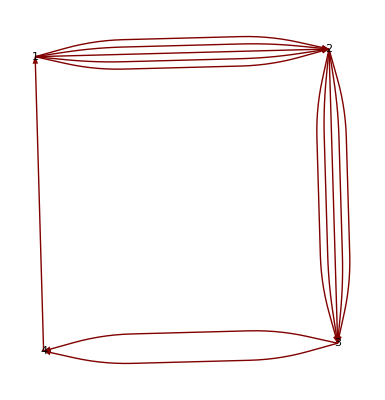

```mathematica
Mat={{0,aa,0,-dd},{-aa,0,bb,0},{0,-bb,0,cc},{dd,0,-cc,0}};
QuiverPlot[Mat]
```

```mathematica
{Mat2,Cvec2,Nvec2}=MutateRight[Mat,Cvec,Nvec,4]
```

{{{0,5,-2,1},{-5,0,5,0},{2,-5,0,-2},{-1,0,2,0}},{501,342,-843,450},{1,1,1,0}}

```mathematica
QCoulomb1=DropFugacity[CoulombBranchFormula[Mat,Cvec,Nvec]];
```

```mathematica
QCoulomb2=OmSToOmS2[DropFugacity[CoulombBranchFormula[Mat2,Cvec2,Nvec2]]];
```

```mathematica
Simplify[{QCoulomb1,QCoulomb2}]
```

{((1+y^2+y^4+y^6)^2)/y^6+OmS[{1,1,1,1},t]+OmS[{1,1,1,2},t],((1+y^2+y^4+y^6)^2)/y^6+OmS2[{1,1,1,0},t]}

```mathematica
Simplify[DropOmSNeg[MutateRightOmS[Mat,4,QCoulomb1]]-QCoulomb2]
```

0

## Examples of generalized quiver mutations

### Example 1 : generalized Kronecker quiver

```mathematica
(* second order semi-primitive wall-crossing formula, from MPS1 *)
Nn=10;
IntToRat={Dp[m_,n_]:>If[{m,n}=={0,0},0,DivisorSum[GCD[m,n],MoebiusMu[#]Omp[m/#,n/#]/#^2 &]],
Dm[m_,n_]:>If[{m,n}=={0,0},0,DivisorSum[GCD[m,n],MoebiusMu[#]Omm[m/#,n/#]/#^2 &]],
Dp[m_,n_,y_]:>If[{m,n}=={0,0},0,DivisorSum[GCD[m,n],MoebiusMu[#](y-1/y)Omp[m/#,n/#,y^#]/#/(y^#-y^(-#)) &]],
Dm[m_,n_,y_]:>If[{m,n}=={0,0},0,DivisorSum[GCD[m,n],MoebiusMu[#](y-1/y)Omm[m/#,n/#,y^#]/#/(y^#-y^(-#)) &]]
};
RatToInt={Omp[m_,n_]:>If[{m,n}=={0,0},0,DivisorSum[GCD[m,n],Dp[m/#,n/#]/#^2 &]],
Omm[m_,n_]:>If[{m,n}=={0,0},0,DivisorSum[GCD[m,n],Dm[m/#,n/#]/#^2 &]],Omp[m_,n_,y_]:>If[{m,n}=={0,0},0,DivisorSum[GCD[m,n],(y-1/y)Dp[m/#,n/#,y^#]/#/(y^#-y^(-#)) &]],
Omm[m_,n_,y_]:>If[{m,n}=={0,0},0,DivisorSum[GCD[m,n],(y-1/y)Dm[m/#,n/#,y^#]/#/(y^#-y^(-#)) &]]};
Zp[m_]:=Sum[Omp[m,n]q^n,{n,0,Nn}];
Zm[m_]:=Sum[Omm[m,n]q^n,{n,0,Nn}];
Zsp1=Exp[Sum[(-1)^(l g12) l g12 Omp[0,l] q^l,{l,0,Nn}]];
Zpmod2=Zp[2]+ 1/2 Sum[(-1)^((j-i)g12) (j-i)g12 Omp[1,i]Omp[1,j] q^(i+j),{i,0,Nn},{j,i+1,Nn}];
Zmmod2=Zm[2]+ 1/2 Sum[(-1)^((j-i)g12) (j-i)g12 Omm[1,i]Omm[1,j] q^(i+j),{j,0,Nn},{i,j+1,Nn}];
Zsp2=Exp[Sum[(-1)^(2l g12)2 l g12 Omp[0,l] q^l,{l,0,Nn}]];
Eq1=Series[Zm[1]-Zp[1] Zsp1,{q,0,Nn}];
soOmm1=Solve[Eq1==0,Table[Omm[1,n],{n,0,Nn}]][[1]];
soOmp1=Solve[Eq1==0,Table[Omp[1,n],{n,0,Nn}]][[1]];
Eq2=Series[Zmmod2-Zpmod2 Zsp2/.soOmm1,{q,0,Nn}];
soOmm2=Solve[Eq2==0,Table[Omm[2,n],{n,0,Nn}]][[1]];
Eq2b=Series[Zmmod2-Zpmod2 Zsp2/.soOmp1,{q,0,Nn}];
soOmp2=Solve[Eq2b==0,Table[Omp[2,n],{n,0,Nn}]][[1]];
```

```mathematica
mm=1;p1=2;q1=3;p2=0;q2=0;M=q1+4q2;
repOmS={ OmS[{0,1},y_,t_]:>q1, OmS[{0,2},y_,t_]:>q2,OmS[{0,n_},y_,t_]:>0/;n>2,OmS[{1,0},y_,t_]:>p1,OmS[{2,0},y_,t_]:>p2,OmS[{n_,0},y_,t_]:>0/;n>2};
```

```mathematica
SemiPrimitive1=Sum[Dm[1,n]q^n,{n,0,Nn}]/.IntToRat/.soOmm2/.soOmm1/.RatToInt/.{Dp[p_,q_]:>OmS[{p,q},y,t],g12->-m}/.repOmS/.OmS[x___]->0/.m->mm
```

2+6 q+6 q^2+2 q^3

```mathematica
SemiPrimitive2=Sum[Dm[2,n]q^n,{n,0,Nn}]/.IntToRat/.soOmm2/.soOmm1/.RatToInt/.{Dp[p_,q_]:>OmS[{p,q},y,t],g12->-m}/.repOmS/.OmS[x___]->0/.m->mm
```

3 q-6 q^2+14 q^3-6 q^4+3 q^5

```mathematica
Simplify[{q^(mm M)(SemiPrimitive1/.q->1/q)/SemiPrimitive1,q^(2mm M)(SemiPrimitive2/.q->1/q)/SemiPrimitive2}]
```

{1,1}

### Example 2 : generalized 3-node quiver without closed loop

```mathematica
aa=1;bb=-1;cc=2;
Nvec={1,4,1};
Cvec={(30 Nvec[[2]]+1)/Nvec[[1]],-80,(50 Nvec[[2]]-1)/Nvec[[3]]};
```

```mathematica
Mat=({{0, aa, -cc}, {-aa, 0, bb}, {cc, -bb, 0}});
$QuiverOmSbasis=0;
$QuiverRecursion=1;
```

```mathematica
(* (a) *)
repOmS={OmS[{0,1,0},y_,t_]:>2,OmS[{0,p_,0},y_,t_]:>0/;p>1};
```

```mathematica
(* (b) *)
repOmS={OmS[{0,1,0},y_,t_]:>3,OmS[{0,p_,0},y_,t_]:>0/;p>1};;
```

```mathematica
(* (c) *)repOmS={OmS[{0,1,0},y_,t_]:>y^2+1+1/y^2,OmS[{0,p_,0},y_,t_]:>0/;p>1};
```

```mathematica
(* (d) *)
repOmS={OmS[{0,1,0},y_,t_]:>4,OmS[{0,p_,0},y_,t_]:>0/;p>1};
```

```mathematica
(* (e) *)
repOmS={OmS[{0,1,0},y_,t_]:>t+1/t,OmS[{0,p_,0},y_,t_]:>0/;p>1};
```

```mathematica
(* (f) *)
repOmS={OmS[{0,2,0},y_,t_]:>1,OmS[{0,p_,0},y_,t_]:>0/;(p>2)||(p==1)};
```

```mathematica
(* (g) *)
repOmS={OmS[{0,2,0},y_,t_]:>-1,OmS[{0,2,0},y_,t_]:>1,OmS[{0,p_,0},y_,t_]:>0/;p>2};
```

```mathematica
$QuiverMutationMult=Sum[k^2OmS[{0,k,0},1,1],{k,0,4}]/.repOmS;
{Mat2,Cvec2,Nvec2}=Simplify[MutateRight[Mat,Cvec,Nvec,2]]
```

{{{0,-1,-2},{1,0,1},{2,-1,0}},{-199,80,-121},{1,4,1}}

```mathematica
QCoulomb1=CoulombBranchFormula[Mat,Cvec,Nvec];
```

CoulombBranchFormula: Constructing Poincaré polynomial...

Evaluating CoulombH factors for dimension vector {0,2,1}

Evaluating CoulombH factors for dimension vector {0,3,0}

Evaluating CoulombH factors for dimension vector {1,1,1}

Evaluating CoulombH factors for dimension vector {1,2,0}

Evaluating CoulombH factors for dimension vector {0,3,1}

Evaluating CoulombH factors for dimension vector {0,4,0}

Evaluating CoulombH factors for dimension vector {1,2,1}

Evaluating CoulombH factors for dimension vector {1,3,0}

Evaluating CoulombH factors for dimension vector {0,4,1}

Evaluating CoulombH factors for dimension vector {1,3,1}

Evaluating CoulombH factors for dimension vector {1,4,0}

CoulombBranchFormula: Substituting CoulombH factors...

```mathematica
QCoulomb2=OmSToOmS2[CoulombBranchFormula[Mat2,Cvec2,Nvec2]];
```

CoulombBranchFormula: Constructing Poincaré polynomial...

Evaluating CoulombH factors for dimension vector {0,2,1}

Evaluating CoulombH factors for dimension vector {0,3,0}

Evaluating CoulombH factors for dimension vector {1,1,1}

Evaluating CoulombH factors for dimension vector {1,2,0}

Evaluating CoulombH factors for dimension vector {0,3,1}

Evaluating CoulombH factors for dimension vector {0,4,0}

Evaluating CoulombH factors for dimension vector {1,2,1}

Evaluating CoulombH factors for dimension vector {1,3,0}

Evaluating CoulombH factors for dimension vector {0,4,1}

Evaluating CoulombH factors for dimension vector {1,3,1}

Evaluating CoulombH factors for dimension vector {1,4,0}

CoulombBranchFormula: Substituting CoulombH factors...

```mathematica
QCoulomb1s=Simplify[MutateLeftOmS2[Mat2,2,DropOmSNeg[MutateRightOmS[Mat,2,QCoulomb1/.repOmS]]]]
```

1/y^5(-(1+2 y^2+4 y^4+4 y^6+2 y^8+y^10) OmS[{0,0,1},y,t] OmS[{1,0,0},y,t]+y (1+y^2+2 y^4+y^6+y^8) OmS[{1,0,1},y,t])

```mathematica
QCoulomb2s=Simplify[MutateRightOmS[Mat,2,DropOmSNeg[MutateLeftOmS2[Mat2,2,QCoulomb2]]/.repOmS]]
```

1/y^5(-(1+2 y^2+4 y^4+4 y^6+2 y^8+y^10) OmS2[{0,0,1},y,t] OmS2[{1,0,0},y,t]+y (1+y^2+2 y^4+y^6+y^8) OmS2[{1,0,1},y,t])

```mathematica
Simplify[DropOmSNeg[MutateLeftOmS2[Mat2,2,QCoulomb2s]]-QCoulomb1s/.repOmS]
```

0

### Example 3 : generalized 3-node quiver with closed loop

```mathematica
aa=2;bb=1;cc=5;
Nvec={1,3,1};
Cvec={(30 Nvec[[2]]+1)/Nvec[[1]],-80,(50 Nvec[[2]]-1)/Nvec[[3]]};
repOmS={OmS[{0,1,0},y_,t_]:>2,OmS[{0,p_,0},y_,t_]:>0/;p>1};
```

```mathematica
Mat=({{0, aa, -cc}, {-aa, 0, bb}, {cc, -bb, 0}});
$QuiverOmSbasis=0;
$QuiverRecursion=1;
```

```mathematica
$QuiverMutationMult=Sum[k^2OmS[{0,k,0},1,1],{k,0,4}]/.repOmS;
{Mat2,Cvec2,Nvec2}=Simplify[MutateRight[Mat,Cvec,Nvec,2]]
```

{{{0,-2,-1},{2,0,-1},{1,1,0}},{-229,80,149},{1,1,1}}

```mathematica
QCoulomb1=CoulombBranchFormula[Mat,Cvec,Nvec];
```

```mathematica
QCoulomb2=OmSToOmS2[CoulombBranchFormula[Mat2,Cvec2,Nvec2]];
```

```mathematica
QCoulomb1s=Simplify[MutateLeftOmS2[Mat2,2,DropOmSNeg[MutateRightOmS[Mat,2,QCoulomb1/.repOmS]]]]
```

(2 (1+y^2)^2 OmS[{0,0,1},y,t] OmS[{1,0,0},y,t])/y^2+OmS[{1,1,1},y,t]+2 OmS[{1,2,1},y,t]

```mathematica
QCoulomb2s=Simplify[MutateRightOmS[Mat,2,DropOmSNeg[MutateLeftOmS2[Mat2,2,QCoulomb2]]/.repOmS]]
```

(2 (1+y^2)^2 OmS2[{0,0,1},y,t] OmS2[{1,0,0},y,t])/y^2+2 OmS2[{1,0,1},y,t]+OmS2[{1,1,1},y,t]

```mathematica
Simplify[DropOmSNeg[MutateLeftOmS2[Mat2,2,QCoulomb2s]]-QCoulomb1s/.repOmS]
```

0